```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/hierarchical chain/

```mathematica
(* Thickness *)
th=0.003;
```

## Diagonalisation directe

### Energy bands

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* bout élémentaire du Hamiltonien périodique *)
Clear[h];
h[n_,k_]:=Block[{tbl,ar},
(* bout libre *)
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+=Transpose[ar];
(* bout périodique *)
ar+=SparseArray[{{1,2^n}->Exp[2^n I k]t[2^(n-1)],{2^n,1}->Exp[- 2^n I k]t[2^(n-1)]}]//Normal
]
```

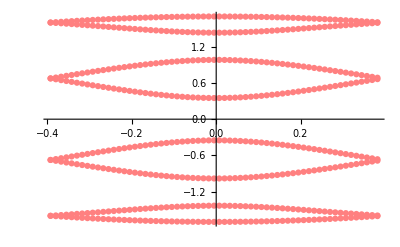

```mathematica
(* energy bands *)
Block[{v=.9,r=.5,listk,dk=.1,i=3,listEk,listH,l},
dk=dk/2^i;
listk=Range[-Pi/2^i,Pi/2^i,dk];
listH=ParallelMap[h[i,#]&,listk];
listEk=ParallelMap[Sort[Eigenvalues[#]]&,listH];
l=MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}];
ListPlot[l,PlotStyle->Directive[Pink]]
]
```

### Wavefunctions, ∀k

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* non periodic part of the Hamiltonian *)
Clear[h];
(* permits us to pass list of arguments to h *)
SetAttributes[h,Listable];
(* we ARBITRARILY set the period to 1, ie we make the change 2^n k -> k *)
h[n_,k_]:=Block[{tbl,ar},
(* bout libre *)
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+=Transpose[ar];
(* bout périodique *)
ar+=SparseArray[{{1,2^n}->Exp[I k]t[2^(n-1)],{2^n,1}->Exp[- I k]t[2^(n-1)]}]//Normal
]
```

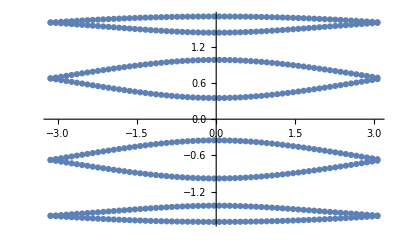

```mathematica
(* energy bands *)
Block[{v=.9,r=.5,listk,dk=.1,i=3,listEk,listH,l},
listk=Range[-Pi,Pi,dk];
listH=h[i,listk];
listEk=ParallelMap[Sort[Eigenvalues[#]]&,listH];
l=Flatten[MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}],1];
ListPlot[l]
]
```

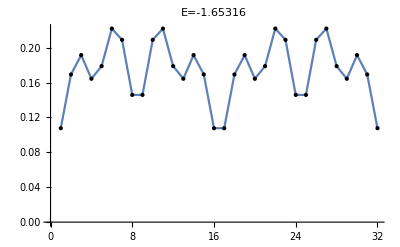

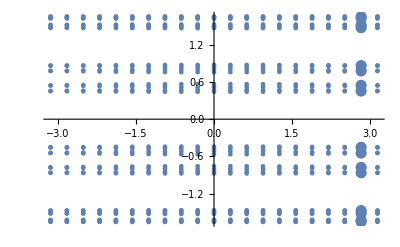

```mathematica
(* wavefunctions *)
Block[{v=.9,r=.5,listk,nk=20,i=5,es,listEk,listWF,l,curk,curvec,tt},
listk=Table[(2.Pi)/nk i,{i,-nk/2,nk/2}];
es=ParallelMap[Eigensystem,h[i,listk]];
{listEk,listWF}={#[[1]]&/@es,#[[2]]&/@es};
l=Flatten[MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}],1];
curk=Floor [nk/2+10];
curvec=2;
tt=Table[it,{it,2^i}];
Print[ListPlot[Abs[listWF[[curk]][[curvec]]],PlotLabel->"E="<>ToString@listEk[[curk]][[curvec]],Joined->True,Epilog->Point/@ MapThread[{#1,#2}&,{tt,Abs@listWF[[curk]][[curvec]]}]]];
Show[ListPlot[l],ListPlot[{listk[[curk]],#}&/@es[[curk]][[1]]]]
]
```

```mathematica
ClearAll[v,r,nk,i,es,listEk,listWF,l,curk,tt];
v=.9;r=.5;nk=20;i=5;
listk=Table[(2.Pi)/nk i,{i,-nk/2,nk/2}];
es=ParallelMap[Eigensystem,h[i,listk]];
{listEk,listWF}={#[[1]]&/@es,#[[2]]&/@es};
l=Flatten[MapThread[Function[e,{#1,e}]/@#2&,{listk,listEk}],1];
tt=Table[it,{it,2^i}];
Manipulate[
curk=Floor [nk/2+j];
GraphicsRow[{ListPlot[Abs[listWF[[curk]][[curvec]]],PlotLabel->"E="<>ToString@listEk[[curk]][[curvec]],Joined->True,Epilog->Point/@ MapThread[{#1,#2}&,{tt,Abs@listWF[[curk]][[curvec]]}]],
ListPlot[l,Epilog->{PointSize[Large],Pink,Point@{listk[[curk]],listEk[[curk]][[curvec]]}}]},ImageSize->Large]
,{j,-nk/2+1,nk/2,1},{curvec,1,2^i,1}]
```

### Wavefunctions, k=0

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
ClearAll[t,r,v];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
SetAttributes[hp,Listable];
hp[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp quand k=0 *)
tbl=Join[tbl,{{1,2^n}->t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
(* Normal convertit en matrice *)
Normal[ar+Transpose[ar]]
]
```

```mathematica
ClearAll[v,r,i,j,e1,wf1,tt1,e2,wf2,tt2];
v=.5;r=.5;i=4;j=i+1;
{{e1,wf1},{e2,wf2}}=ParallelMap[Eigensystem,hp[{i,j}]];
tt1=Table[it,{it,2^i}];tt2=Table[it,{it,2^j}];
Manipulate[
GraphicsGrid[{{ListPlot[wf1[[v1]],PlotLabel->"E_1="<>ToString@e1[[v1]],Joined->True,Epilog->Point/@ MapThread[{#1,#2}&,{tt1,wf1[[v1]]}]],ListPlot[e1,Epilog->{PointSize[Large],Pink,Point@{tt1[[v1]],e1[[v1]]}}]},
{ListPlot[wf2[[v2]],PlotLabel->"E_2="<>ToString@e2[[v2]],Joined->True,Epilog->Point/@ MapThread[{#1,#2}&,{tt2,wf2[[v2]]}]],ListPlot[e2,Epilog->{PointSize[Large],Pink,Point@{tt2[[v2]],e2[[v2]]}}]}},ImageSize->Large]
,{v1,1,2^i,1},{v2,1,2^j,1}]
```